## Eq. (6): Stationary distribution of the mating type number vector n

```mathematica
(* For full derivation, see Constable and Kokko, Nature Ecology and Evolution, 2018 (see derivation of Eq.(S35) within) *)

(* Define vector n^↓ (vector n reordered with largest entries first) *)
nArrow[n_]:=DeleteCases[Reverse[Sort[n]],0]

(* Define stationary distribution Subscript[(P^st), n] (see Eq. 6 with b(k) and d(k) substituted from Eq. 5) *)
PST[n_]:=(*1/(Mmax - Length[nArrow[n]])*)(2*m*NT((NT((1+c)/(1-c)))!)1/(1+c))^(Length[nArrow[n]]-1)(((2NT*c)/(1-c))!)Product[1/(nArrow[n][[i]])1/((NT(1+c)/(1-c)-nArrow[n][[i]])!),{i,1,Length[nArrow[n]]}]
(* Note that the mutation normalisation term in the above expression has here been suppressed for plotting clarity *)
```

## Eq. (9) and code for generating Fig. 1

```mathematica
(* Define approximation for stationary distribution of the number of mating types Subscript[(P^st), M] ( see Eq.(9); for full derivation see Section S.3). *)
PSTMApprox[M_]:=(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT;
```

### Load obligately sexual data (c=0) for plot

```mathematica
(* Simulation data for PSTM is generated by running compiled c++ file MT_sim_compiled (as in Mathematica section "Code for generating plots in Fig. S1") and sampling regularly over long time windows (see timestamps in .txt files, measured in units of generations) *)

(* Define two seperate population sizes for data *)
NTList=Table[NT,{NT,2000,4000,2000}];

(* Define two vectors for storing Subscript[(P^st), M] distributions for obligately sexual case (one simulated, one analytic) *)
MSimHistoTableOb=ConstantArray[0,Length[NTList]];
MAnaHistoTableOb=ConstantArray[0,Length[NTList]];

(* Loop over two possible population sizes *)
For[iN=1,iN≤Length[NTList],iN++,

(* Define parameters used for data [c=0,m=10^-8] *)
params={c->0,Mmax->100,m->0.00000001,NT->NTList[[iN]]};

(* Define file directory for import data *)
importDirectory=NotebookDirectory[]<>"Data/Fig1/Fig_1_c_0_N_"<>ToString[AccountingForm[NT/.params]]<>"_M_traj.txt";

(* Import data *)
MTrajImport=Flatten[Import[importDirectory,"Table"]];

(* Fill simulation and analytic vectors for storing Subscript[(P^st), M]: note normalization of simulation results *)
MSimHistoTableOb[[iN]]=Table[{M,Count[MTrajImport,M]/Length[MTrajImport]},{M,1,20}];
MAnaHistoTableOb[[iN]]=Table[{M,PSTMApprox[M]/.params},{M,2,20}];

];

(* Normalise analytic vectors for  Subscript[(P^st), M] *)
For[i=1,i≤Length[MAnaHistoTableOb],i++,
MAnaHistoTableOb[[i]][[All,2]]=(MAnaHistoTableOb[[i]][[All,2]])/Total[MAnaHistoTableOb[[i]][[All,2]]];
]
```

### Load facultatively sexual data (c=0.8) for plot

```mathematica
(* Simulation data for PSTM is generated by running compiled c++ file MT_sim_compiled (as in Mathematica section "Code for generating plots in Fig. S1") and sampling regularly over long time windows (see timestamps in .txt files, measured in units of generations) *)

(* Define two seperate population sizes for data *)
NTList=Table[NT,{NT,2000,4000,2000}];

(* Define two vectors for storing Subscript[(P^st), M] distributions for facultatively sexual case (one simulated, one analytic) *)
MSimHistoTableFac=ConstantArray[0,Length[NTList]];
MAnaHistoTableFac=ConstantArray[0,Length[NTList]];

(* Loop over two possible population sizes *)
For[iN=1,iN≤Length[NTList],iN++,

(* Define parameters used for data [c=0.8,m=10^-8] *)
params={c->0.8,Mmax->100,m->0.00000001,NT->NTList[[iN]]};

(* Define file directory for import data *)
importDirectory=NotebookDirectory[]<>"Data/Fig1/Fig_1_c_08_N_"<>ToString[AccountingForm[NT/.params]]<>"_M_traj.txt";

(* Import data *)
MTrajImport=Flatten[Import[importDirectory,"Table"]];

(* Fill simulation and analytic vectors for storing Subscript[(P^st), M]: note normalization of simulation results *)
MSimHistoTableFac[[iN]]=Table[{M,Count[MTrajImport,M]/Length[MTrajImport]},{M,1,20}];
MAnaHistoTableFac[[iN]]=Table[{M,PSTMApprox[M]/.params},{M,2,20}];

];

(* Normalise analytic vectors for  Subscript[(P^st), M] *)
For[i=1,i≤Length[MAnaHistoTableFac],i++,
MAnaHistoTableFac[[i]][[All,2]]=(MAnaHistoTableFac[[i]][[All,2]])/Total[MAnaHistoTableFac[[i]][[All,2]]];
]
```

### Compile plot

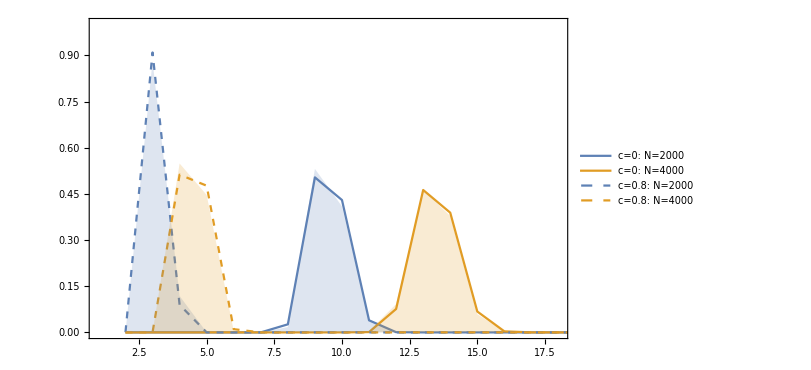

```mathematica
Show[
ListLinePlot[MAnaHistoTableOb,PlotRange->{{1,18},{0,1}},PlotLegends->{"c=0: N=2000","c=0: N=4000"},Frame->True,ImageSize->600,FrameStyle->18],
ListLinePlot[MAnaHistoTableFac,PlotRange->All,PlotStyle->Dashed,PlotLegends->{"c=0.8: N=2000","c=0.8: N=4000"}],
ListLinePlot[MSimHistoTableOb,PlotRange->All,PlotStyle->None,Filling->Bottom],
ListLinePlot[MSimHistoTableFac,PlotRange->All,PlotStyle->None,Filling->Bottom]
]
```

## Code for generating Fig. 2

### Analytic results

```mathematica
(* Define rApprox as defined in Eq.(11) *)
rApprox[M_]:=PSTMApprox[M]/PSTMApprox[M-1];

(* Define mCrit(M), the critical value of m needed for the mode of PstM to be at least M *)
mgCritApprox[M_]:=Collect[NT*m/rApprox[M],m];
```

### Density plot - obligate sex (c=0)

```mathematica
(* Define table storing the mode of Subscript[(P^st), M] (Subscript[M, o] in the main text), to be calculated numerically. First two elements store exponent numbers (see code below) *)
ModePSTMTable=Flatten[Table[Table[{NTEXP,-mgEXP,0},{NTEXP,5,7,2/20}],{mgEXP,4,10,6/20}],1];

(* Define parameters: dM is the step size in M when numerically calculating Subscript[M, o] [see Eq.(12)] *)
params={c->0,NT->NT,m->m,Mmax->1400,dM->1};

(* Loop over the vector of Subscript[M, o] values (ModePSTMTable) to numerically calculate Subscript[M, o] for each combination of parameters N and m *)
For[i=1,i≤Length[ModePSTMTable],i++,

(* Set loop population size *)
params[[2]]=NT->10^ModePSTMTable[[i,1]];

(* Set loop mutation rate (notice scaling from per-generation mutation rate, Subscript[m, g]) *)
params[[3]]=m->10^ModePSTMTable[[i,2]]/10^ModePSTMTable[[i,1]];(* Subscript[m, g] = m*N -> m=mg/NT *)

(* Set initial Subscript[M, o] value for loop ... ) *)
Mt=2.01;

(* Test whether r < 1; if so break ... *)
While[
(rApprox[Mt]/.params)>1&&Mt≤Mmax/.params,
Mt=Mt+dM/.params
];
(* Subscript[M, o] is last value of M for which Subscript[r, M] > 1 -- therefore subtract 1 *)
Mt=Mt-1;

(* Log resultant value of Mt for plot *)
ModePSTMTable[[i,3]]=Log[Mt];

];
```

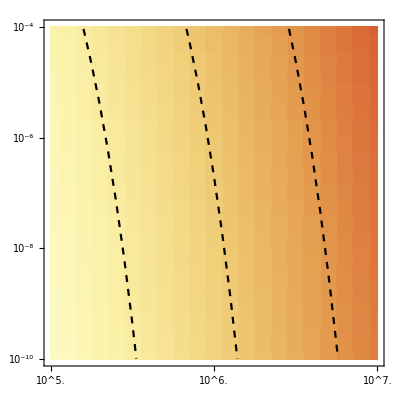

```mathematica
(* Define styling to convert from table (where everything is logged) to actual numbers *)
logBarMinMax={0,Log[600]};
frameTicksStyling={
{Table[{-mgEXP,If[Mod[mgEXP,2]==0,Superscript[10,ToString[-mgEXP]],""]},{mgEXP,4,10}],None},
{Table[{NTEXP,If[Mod[NTEXP,1]==0,Superscript[10,ToString[NTEXP]],""]},{NTEXP,5,7,0.2}],None}};

(* Make plot with "contour lines" of Subscript[M, o]={80,160,320} using mgCritApprox function *)
plotModeMPanelA=Show[
ListDensityPlot[ModePSTMTable,InterpolationOrder->0,PlotRange->All,(*PlotLegends->Automatic,*)ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),FrameTicks->frameTicksStyling,
FrameTicksStyle->{{18,18},{18,18}},ImageSize->400],
ListLinePlot[
Table[
Table[{NTEXP,1/Log[mgCritApprox[M]/.c->0/.NT->10^NTEXP,10]},{NTEXP,5,7,0.05}],
{M,{80,160,320}}
]
,PlotStyle->{{Black,Dashed}},PlotRange->{1/Log[10^-10/0.97,10],1/Log[10^-4/1.1,10]}]
]

(* Generate legend for plot *)
plotLegend=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),logBarMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Column",
"Ticks"->{{0,"1"},{Log[10],"10"},{Log[100],"100"},{Log[600],"600"}},
TicksStyle->18,ImageSize->800]
```

### Density plot - obligate sex (c=0.9)

```mathematica
(*Table[Table[{10^NTEXP,10^-mgEXP,0},{NTEXP,5,7,2/10}],{mgEXP,-10,-2,8/10}];*)
ModePSTMTable=Flatten[Table[Table[{NTEXP,-mgEXP,0},{NTEXP,5,7,2/20}],{mgEXP,4,10,6/20}],1];

params={c->0.9,NT->NT,m->m,Mmax->1400,dM->1};
For[i=1,i≤Length[ModePSTMTable],i++,
params[[2]]=NT->10^ModePSTMTable[[i,1]];
params[[3]]=m->10^ModePSTMTable[[i,2]]/10^ModePSTMTable[[i,1]];(* Subscript[m, g] = m*N -> m=mg/NT *)

Mt=2.01;
While[
(rApprox[Mt]/.params)>1&&Mt≤Mmax/.params,
Mt=Mt+dM/.params
];
Mt=Mt-1;
If[Mt==Mmax+0.01/.params,Mt=2];

ModePSTMTable[[i,3]]=Log[Mt];
(*Print["i is "<>ToString[i]<>"; Mt is "<>ToString[Mt] ];*)

];
```

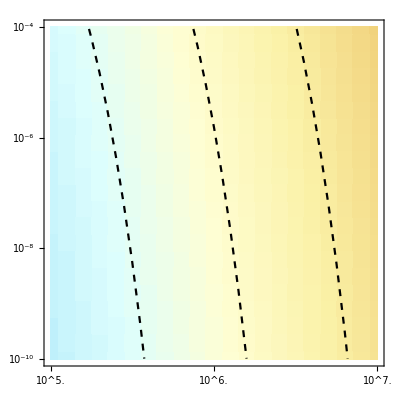

```mathematica
(* Define styling to convert from table (where everything is logged) to actual numbers *)

logBarMinMax={0,Log[600]};

frameTicksStyling={
{Table[{-mgEXP,If[Mod[mgEXP,2]==0,Superscript[10,ToString[-mgEXP]],""]},{mgEXP,4,10}],None},
{Table[{NTEXP,If[Mod[NTEXP,1]==0,Superscript[10,ToString[NTEXP]],""]},{NTEXP,5,7,0.2}],None}};

plotModeMPanelB=Show[
ListDensityPlot[ModePSTMTable,InterpolationOrder->0,PlotRange->All,(*PlotLegends->Automatic,*)ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),FrameTicks->frameTicksStyling,
FrameTicksStyle->{{18,18},{18,18}},ImageSize->400],
ListLinePlot[
Table[
Table[{NTEXP,1/Log[mgCritApprox[M]/.c->0.9/.NT->10^NTEXP,10]},{NTEXP,5,7,0.05}],
{M,{20,40,80}}
]
,PlotStyle->{{Black,Dashed}},PlotRange->{1/Log[10^-10/0.97,10],1/Log[10^-4/1.1,10]}]
]

(* Whether the log[4] bit is in there or not is changing the ordering of the labels!! *)
plotLegend=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),logBarMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Column",
"Ticks"->{{0,"1"},{Log[10],"10"},{Log[100],"100"},{Log[600],"600"}},
TicksStyle->18,ImageSize->800]
```

### Density plot - obligate sex (c=0.99)

```mathematica
(*Table[Table[{10^NTEXP,10^-mgEXP,0},{NTEXP,5,7,2/10}],{mgEXP,-10,-2,8/10}];*)
ModePSTMTable=Flatten[Table[Table[{NTEXP,-mgEXP,0},{NTEXP,5,7,2/40}],{mgEXP,4,10,6/40}],1];

params={c->0.99,NT->NT,m->m,Mmax->1400,dM->1};
For[i=1,i≤Length[ModePSTMTable],i++,
params[[2]]=NT->10^ModePSTMTable[[i,1]];
params[[3]]=m->10^ModePSTMTable[[i,2]]/10^ModePSTMTable[[i,1]];(* Subscript[m, g] = m*N -> m=mg/NT *)

Mt=1.01;
While[
(rApprox[Mt]/.params)>1&&Mt≤Mmax/.params,
Mt=Mt+dM/.params
];
Mt=Mt-1;
If[Mt==Mmax+0.5/.params,Mt=1.01];

ModePSTMTable[[i,3]]=Log[Mt-0.01];
(*Print["i is "<>ToString[i]<>"; Mt is "<>ToString[Mt] ];*)

];
```

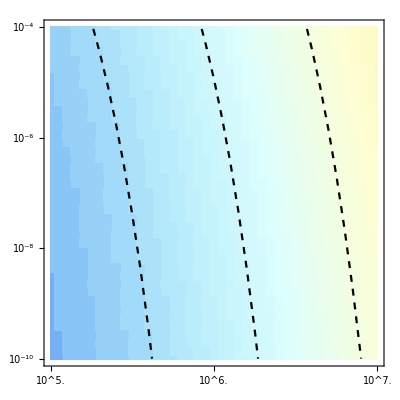

```mathematica
(* Define styling to convert from table (where everything is logged) to actual numbers *)

logBarMinMax={0,Log[600]};

frameTicksStyling={
{Table[{-mgEXP,If[Mod[mgEXP,2]==0,Superscript[10,ToString[-mgEXP]],""]},{mgEXP,4,10}],None},
{Table[{NTEXP,If[Mod[NTEXP,1]==0,Superscript[10,ToString[NTEXP]],""]},{NTEXP,5,7,0.2}],None}};

plotModeMPanelC=Show[
ListDensityPlot[ModePSTMTable,InterpolationOrder->0,PlotRange->All,(*PlotLegends->Automatic,*)ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),FrameTicks->frameTicksStyling,
FrameTicksStyle->{{18,18},{18,18}},ImageSize->400],
ListLinePlot[
Table[
Table[{NTEXP,1/Log[mgCritApprox[M]/.c->0.99/.NT->10^NTEXP,10]},{NTEXP,5,7,0.05}],
{M,{7,14,28}}
]
,PlotStyle->{{Black,Dashed}},PlotRange->{1/Log[10^-10/0.97,10],1/Log[10^-4/1.1,10]}]
]

(* Whether the log[4] bit is in there or not is changing the ordering of the labels!! *)
plotLegend=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),logBarMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Column",
"Ticks"->{{0,"1"},{Log[10],"10"},{Log[100],"100"},{Log[600],"600"}},
TicksStyle->18,ImageSize->800]
```

### Density plot - obligate sex (c=0.999)

```mathematica
(*Table[Table[{10^NTEXP,10^-mgEXP,0},{NTEXP,5,7,2/10}],{mgEXP,-10,-2,8/10}];*)
ModePSTMTable=Flatten[Table[Table[{NTEXP,-mgEXP,0},{NTEXP,5,7,2/40}],{mgEXP,4,10,6/40}],1];

params={c->0.999,NT->NT,m->m,Mmax->1400,dM->1};
For[i=1,i≤Length[ModePSTMTable],i++,
params[[2]]=NT->10^ModePSTMTable[[i,1]];
params[[3]]=m->10^ModePSTMTable[[i,2]]/10^ModePSTMTable[[i,1]];(* Subscript[m, g] = m*N -> m=mg/NT *)

Mt=1.01;
While[
(rApprox[Mt]/.params)>1&&Mt≤Mmax/.params,
Mt=Mt+dM/.params
];
Mt=Mt-1;
If[Mt==Mmax+0.01/.params,Mt=1.01];

ModePSTMTable[[i,3]]=Log[Mt-0.01];


];
```

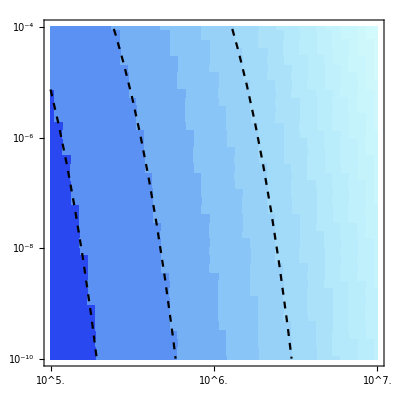

```mathematica
(* Define styling to convert from table (where everything is logged) to actual numbers *)

logBarMinMax={0,Log[600]};

frameTicksStyling={
{Table[{-mgEXP,If[Mod[mgEXP,2]==0,Superscript[10,ToString[-mgEXP]],""]},{mgEXP,4,10}],None},
{Table[{NTEXP,If[Mod[NTEXP,1]==0,Superscript[10,ToString[NTEXP]],""]},{NTEXP,5,7,0.2}],None}};

plotModeMPanelD=Show[
ListDensityPlot[ModePSTMTable,InterpolationOrder->0,PlotRange->All,(*PlotLegends->Automatic,*)ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),FrameTicks->frameTicksStyling,
FrameTicksStyle->{{18,18},{18,18}},ImageSize->400],
ListLinePlot[
Table[
Table[{NTEXP,1/Log[mgCritApprox[M]/.c->0.999/.NT->10^NTEXP,10]},{NTEXP,5,7,0.05}],
{M,{2,3,6}}
]
,PlotStyle->{{Black,Dashed}},PlotRange->{1/Log[10^-10/0.97,10],1/Log[10^-4/1.1,10]}]
]

(* Whether the log[4] bit is in there or not is changing the ordering of the labels!! *)
plotLegend=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),logBarMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Column",
"Ticks"->{{0,"1"},{Log[10],"10"},{Log[100],"100"},{Log[600],"600"}},
TicksStyle->18,ImageSize->800]
```

## Code for generating Fig 3

```mathematica
QEst[M_]=((1-c)/(1+c))1/(M-1);
```

### Load Data and plot

```mathematica
(* Fixation probability data is generated using the compiled c++ code MT_sim_compiled with N=100,001 and c={0,0.9,0.99,0.999} averaged over 10^3 (c=0), 10^4 (c=0.9 and c=0.99) and 10^5 runs (c=0.999) *)
```

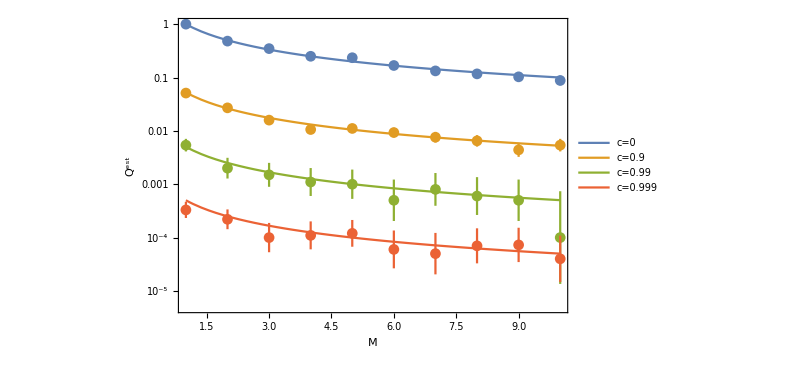

```mathematica
params={NT->100001,m->0,c->0,Mmax->50,mutSD->0};

(* Load data from file *)
fixProbFuncRc0=Import[NotebookDirectory[]<>"Data/Fig3/Fig_3_fixprob_c_0.txt","Table"];
fixProbFuncRc09=Import[NotebookDirectory[]<>"Data/Fig3/Fig_3_fixprob_c_09.txt","Table"];
fixProbFuncRc099=Import[NotebookDirectory[]<>"Data/Fig3/Fig_3_fixprob_c_099.txt","Table"];
fixProbFuncRc0999=Import[NotebookDirectory[]<>"Data/Fig3/Fig_3_fixprob_c_0999.txt","Table"];

(* Plot data against analytic prediction: note that Wald-type confidence intervals are used for error bars: err = √(2 Subscript[p, est](1-Subscript[p, est])/Subscript[N, samples]) *)
Needs["ErrorBarLogPlots`"]
Show[
LogPlot[
{
QEst[R+1]/.c->0,
QEst[R+1]/.c->0.9,
QEst[R+1]/.c->0.99,
QEst[R+1]/.c->0.999
},{R,1,10},AxesOrigin->{1,0.5*10^-5},Frame->True,PlotLegends->LineLegend[Automatic,{"c=0","c=0.9","c=0.99","c=0.999"}],ImageSize->600,FrameStyle->18,FrameLabel->{{"Q^est",None},{"M",None}}
],
ErrorListLogPlot[
{Table[Join[fixProbFuncRc0[[i]],{2 √((fixProbFuncRc0[[i,2]](1-fixProbFuncRc0[[i,2]]))/1000)}],{i,1,10}],
Table[Join[fixProbFuncRc09[[i]],{2 √((fixProbFuncRc09[[i,2]](1-fixProbFuncRc09[[i,2]]))/10000)}],{i,1,10}],
Table[Join[fixProbFuncRc099[[i]],{2 √((fixProbFuncRc099[[i,2]](1-fixProbFuncRc099[[i,2]]))/10000)}],{i,1,10}],
Table[Join[fixProbFuncRc0999[[i]],{2 √((fixProbFuncRc0999[[i,2]](1-fixProbFuncRc0999[[i,2]]))/100000)}],{i,1,10}]
}
]
]
```

## Code for generating Fig. 4

```mathematica
(* Define Subscript[r, M] [see Eq.(11)] *)
r[M_]:=√(2 π)(2 m)/(1+c)√NT((M-1)/M)^(3/2-M)θ^(1/2+NT θ)((θ-1/M)/(θ-1/(M-1)))^(-1/2) ((θ-1/M)/(θ-1/(M-1)))^((1-M* θ)NT)(θ-1/(M-1))^(-NT*θ);

(* Define Subscript[T, M]^Ext [see Eq.(18)] *)
TExt[M_]:=1/NT(M-1)/m θ*r[M];

(* Define Subscript[T, M]^Neutral [see Eq.(19)] *)
TExtNeutral[M_]:=-NT*Sum[(-1)^(s-1)Binomial[M,s] s/M Log[s/M],{s,1,M-1}];

(* Define gradients defining conditions under which we expect either Subscript[T, M]^Ext or Subscript[T, M]^Neutral to be a better approximation of the extinction time *)
dTExtdN[M_]=D[TExt[M]/.θ->(1+c)/(1-c),NT];
dTExtdc[M_]=D[TExt[M]/.θ->(1+c)/(1-c),c];
dTExtdM[M_]=D[TExt[MD]/.θ->(1+c)/(1-c),MD]/.MD->M;

(* Extinction time data obtained using compiled c++ code MT_sim_compiled - Data averaged over 10^4 runs for each data point *)
```

### Load extinction time data: c=0.1 ,M_0=2

```mathematica
Clear[M0]
params={M->2,c->0.1,maxRuns->10000};

fixTimeSimTableM2c01=Join[Table[{NT,0,0},{NT,6,24,(24-6)/(4-1)}],Table[{NT,0,0},{NT,{36,48}}]];

For[i=1,i≤Length[fixTimeSimTableM2c01],i++,

simData=Flatten[Import[NotebookDirectory[]<>"Data/Fig4/Fig_4_c_"<>ToString[c/.params]<>"_M_"<>ToString[M/.params]<>"_N_"<>ToString[fixTimeSimTableM2c01[[i,1]]]<>".txt","Table"],1];

fixTimeSimTableM2c01[[i,2]]=Mean[simData];
fixTimeSimTableM2c01[[i,3]]=StandardDeviation[simData]/.NT->fixTimeSimTableM2c01[[i,1]];

];
```

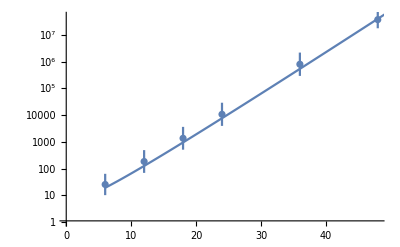

```mathematica
Show[
ErrorListLogPlot[fixTimeSimTableM2c01,PlotRange->{1,5*10^7}],
LogPlot[
{If[((dTExtdN[M]>0)/.{M->2.01,c->0.1}),N[(TExt[M]/.θ->(1+c)/(1-c)/.M->2.01)/.c->0.1],TExtNeutral[M]/.M->2]
},{NT,6,50},AxesOrigin->{0,1},PlotRange->All,Frame->True]
]
```

### Load extinction time data: c=0.1 ,M_0=3

```mathematica
Clear[M0]
params={M->3,c->0.1,maxRuns->10000};

fixTimeSimTableM3c01=Join[Table[{NT,0,0},{NT,6,90,(90-6)/(4-1)}],Table[{NT,0,0},{NT,{105,150}}]];

For[i=1,i≤Length[fixTimeSimTableM3c01],i++,

simData=Flatten[Import[NotebookDirectory[]<>"Data/Fig4/Fig_4_c_"<>ToString[c/.params]<>"_M_"<>ToString[M/.params]<>"_N_"<>ToString[fixTimeSimTableM3c01[[i,1]]]<>".txt","Table"],1];

fixTimeSimTableM3c01[[i,2]]=Mean[simData];
fixTimeSimTableM3c01[[i,3]]=StandardDeviation[simData]/.NT->fixTimeSimTableM3c01[[i,1]];

];
```

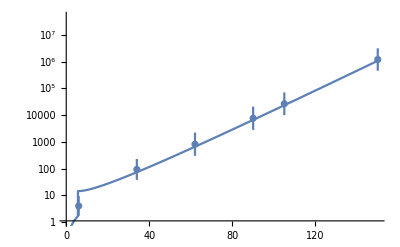

```mathematica
Show[
ErrorListLogPlot[fixTimeSimTableM3c01,PlotRange->{1,5*10^7}],
LogPlot[
{If[((dTExtdN[M]>0)/.{M->3,c->0.1}),N[(TExt[M]/.θ->(1+c)/(1-c)/.M->3)/.c->0.1],TExtNeutral[M]/.M->3]
},{NT,2,150},AxesOrigin->{0,1},PlotRange->All,Frame->True]
]
```

### Load extinction time data: c=0.1 ,M_0=4

```mathematica
Clear[M0]
params={M->4,c->0.1,maxRuns->10000};

fixTimeSimTableM4c01=Join[Table[{NT,0,0},{NT,8,104,(104-8)/(4-1)}],Table[{NT,0,0},{NT,{132,160}}]];;

For[i=1,i≤Length[fixTimeSimTableM4c01],i++,

simData=Flatten[Import[NotebookDirectory[]<>"Data/Fig4/Fig_4_c_"<>ToString[c/.params]<>"_M_"<>ToString[M/.params]<>"_N_"<>ToString[fixTimeSimTableM4c01[[i,1]]]<>".txt","Table"],1];

fixTimeSimTableM4c01[[i,2]]=Mean[simData];
fixTimeSimTableM4c01[[i,3]]=StandardDeviation[simData]/.NT->fixTimeSimTableM4c01[[i,1]];

];
```

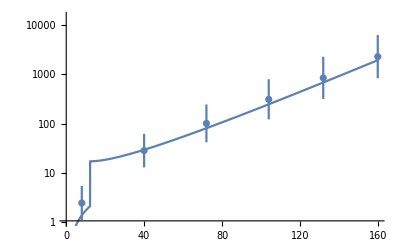

```mathematica
Show[
ErrorListLogPlot[fixTimeSimTableM4c01,PlotRange->{1,1.5*10^4}],
LogPlot[
{If[((dTExtdN[M]>0)/.{M->4,c->0.1}),N[(TExt[M]/.θ->(1+c)/(1-c)/.M->4)/.c->0.1],TExtNeutral[M]/.M->4]
},{NT,2,160},AxesOrigin->{0,1},PlotRange->All,Frame->True]
]
```

### Load extinction time data: c=0.9 ,M_0=2

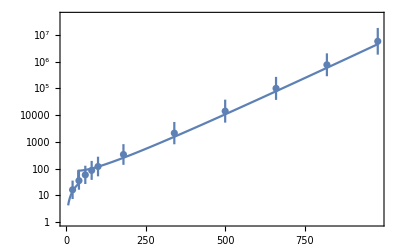

```mathematica
(* List key parameters *)
Clear[M0]
params={M->2,c->0.9,maxRuns->10000};

(* List of initial population sizes *)
fixTimeSimTableM2=Join[Table[{NT,0,0},{NT,20,100,20}],Table[{NT,0,0},{NT,180,500,(500-20)/(4-1)}],Table[{NT,0,0},{NT,{660,820,980}}]];
(* Import data and calculate mean extinction time and variance in extinction time *)
For[i=1,i≤Length[fixTimeSimTableM2],i++,

simData=Flatten[Import[NotebookDirectory[]<>"Data/Fig4/Fig_4_c_"<>ToString[c/.params]<>"_M_"<>ToString[M/.params]<>"_N_"<>ToString[fixTimeSimTableM2[[i,1]]]<>".txt","Table"],1];

fixTimeSimTableM2[[i,2]]=Mean[simData];
fixTimeSimTableM2[[i,3]]=StandardDeviation[simData]/.NT->fixTimeSimTableM2[[i,1]];

];

(* Plot data against analytic prediction from Eq. (20) *)
Needs["ErrorBarPlots`"]
Show[
LogPlot[
{If[((dTExtdN[M]>0)/.{M->2.01,c->0.9}),N[(TExt[M]/.θ->(1+c)/(1-c)/.M->2.01)/.c->0.9],TExtNeutral[M]/.M->2]
},{NT,6,980},AxesOrigin->{0,1},PlotRange->{1,5*10^7},Frame->True],
ErrorListLogPlot[{fixTimeSimTableM2}]
]
```

### Load extinction time data: c=0.9, M_0=3

```mathematica
Clear[M0]
params={M->3,c->0.9,maxRuns->10000};

fixTimeSimTableM3=Join[Table[{NT,0,0},{NT,48,258,30}],Table[{NT,0,0},{NT,20,1220,(1220-20)/(4-1)}],Table[{NT,0,0},{NT,{1620,2020}}]];

For[i=1,i≤Length[fixTimeSimTableM3],i++,

simData=Flatten[Import[NotebookDirectory[]<>"Data/Fig4/Fig_4_c_"<>ToString[c/.params]<>"_M_"<>ToString[M/.params]<>"_N_"<>ToString[fixTimeSimTableM3[[i,1]]]<>".txt","Table"],1];

fixTimeSimTableM3[[i,2]]=Mean[simData];
fixTimeSimTableM3[[i,3]]=StandardDeviation[simData]/.NT->fixTimeSimTableM3[[i,1]];

];
```

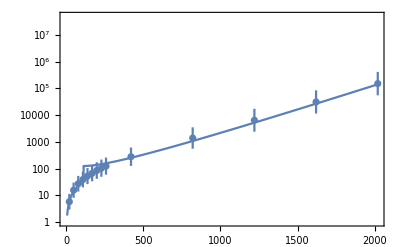

```mathematica
Show[
LogPlot[
{If[((dTExtdN[M]>0)/.{M->3,c->0.9}),N[(TExt[M]/.θ->(1+c)/(1-c)/.M->3)/.c->0.9],TExtNeutral[M]/.M->3]
},{NT,6,2020},AxesOrigin->{0,1},PlotRange->{1,5*10^7},Frame->True],
ErrorListLogPlot[{fixTimeSimTableM3}]
]
```

### Load extinction time data: c=0.9, M_0=4

```mathematica
Clear[M0]
params={M->4,c->0.9,maxRuns->10000};

fixTimeSimTableM4=Join[Table[{NT,0,0},{NT,40,340,40}],Table[{NT,0,0},{NT,20,1220,(1220-20)/(4-1)}],Table[{NT,0,0},{NT,{1620,2020}}]];

For[i=1,i≤Length[fixTimeSimTableM4],i++,

simData=Flatten[Import[NotebookDirectory[]<>"Data/Fig4/Fig_4_c_"<>ToString[c/.params]<>"_M_"<>ToString[M/.params]<>"_N_"<>ToString[fixTimeSimTableM4[[i,1]]]<>".txt","Table"],1];

fixTimeSimTableM4[[i,2]]=Mean[simData];
fixTimeSimTableM4[[i,3]]=StandardDeviation[simData]/.NT->fixTimeSimTableM4[[i,1]];

];
```

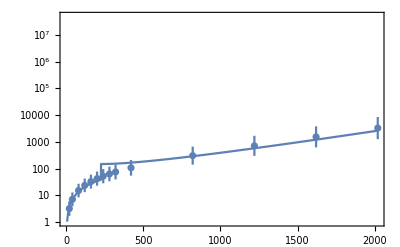

```mathematica
Show[
LogPlot[
{If[((dTExtdN[M]>0)/.{M->4,c->0.9}),N[(TExt[M]/.θ->(1+c)/(1-c)/.M->4)/.c->0.9],TExtNeutral[M]/.M->4]
},{NT,6,2020},AxesOrigin->{0,1},PlotRange->{1,5*10^7},Frame->True],
ErrorListLogPlot[{fixTimeSimTableM4}]
]
```

## Code for generating Fig. 5

#### c=0

```mathematica
(* Define extinction time table for different N and M values (note that N and M values in tables are exponents for ease of plotting) *)
TExtTable=Flatten[Table[Table[{NTEXP,M,0},{NTEXP,3,7,2/20}],{M,2,20,1}],1];

(* Define table indicating whether extinction time should be calculated neutrally or not (0 for non-neutral, 1 for neutral) *)
NeutralLimitTable=Flatten[Table[Table[{NTEXP,M,0},{NTEXP,3,7,2/20}],{M,2,20,1}],1];

(* Define table indicating whether extinction time exceeds a certain value (set to 10^11 generations below - approx evolutionary age of fungi) *)
OldLimitTable=Flatten[Table[Table[{NTEXP,M,0},{NTEXP,3,7,2/20}],{M,2,20,1}],1];

(* Define parameters - set c very small (approx 0) to avoid numerical evaluation errors near c=0 *)
params={c->10^-3,NT->NT,M->M,TMax->10^11};

(* Loop over N and M parameter values *)
For[i=1,i≤Length[TExtTable],i++,

(* Set parameters *)
params[[2]]=NT->10^TExtTable[[i,1]]+1.21;
params[[3]]=M->TExtTable[[i,2]];

(* If NT is less than 10^5, extinction is approximately neutral - this line simply speeds up the code for checking neutral values, and can be removed to confirm assertation *)
If[(NT/.params)<10^5,
TExtTable[[i,3]]=If[((dTExtdN[M]>0)/.params),N[Log[Log[N[TExt[M]/.θ->(1+c)/(1-c)/.params]]]],N[Log[Log[TExtNeutral[M]/.params]]]];,
TExtTable[[i,3]]=Log[Log[10*TMax/.params]];
];
(* Note that in above the double logarithm of the fixation time is taken *)

(* Evaluate tables tracking regions of parameter space that are neutral or where the extinction time exceeds large threshold *)
NeutralLimitTable[[i,3]]=If[((dTExtdN[M]>0)/.params),0,1];
OldLimitTable[[i,3]]=If[TExtTable[[i,3]]<Log[Log[TMax/.params]],0,1];

];
```

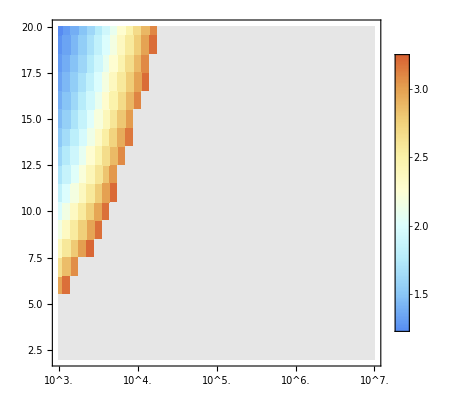

```mathematica
(* Construct plot of above-generated data *)

logBarMinMax={1,Log[Log[2*10^11]]};

frameTicksStyling={
{Automatic,None},
{Table[{NTEXP,If[Mod[NTEXP,1]==0,Superscript[10,ToString[NTEXP]],""]},{NTEXP,3,7,0.2}],None}};

plotTExtPanelA=
Show[
ListDensityPlot[TExtTable,InterpolationOrder->0,PlotRange->{All,All,logBarMinMax},PlotLegends->Automatic,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),FrameTicks->frameTicksStyling,
FrameTicksStyle->{{18,18},{18,18}},ImageSize->400],
ListContourPlot[NeutralLimitTable,PlotRange->All,InterpolationOrder->1,Contours->{-1,1},ContourShading->None,ContourStyle->Directive[{Thick,Blue,Dashed}]],
ListContourPlot[OldLimitTable,PlotRange->All,InterpolationOrder->0,Contours->{-1,1},ContourShading->{{Lighter[LightGray]},{None}}]
]

plotLegend=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),logBarMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Column",
"Ticks"->{
{N[Log[Log[10^2]]],"10^2"},
{N[Log[Log[10^3]]],"10^3"},
{N[Log[Log[10^5]]],"10^5"},
{N[Log[Log[10^7]]],"10^7"},
{N[Log[Log[10^9]]],"10^9"},
{N[Log[Log[10^11]]],"10^11"}
}
,
TicksStyle->18,ImageSize->800]
```

#### c=0.9

```mathematica
(* Define extinction time table for different N and M values (note that N and M values in tables are exponents for ease of plotting) *)
TExtTable=Flatten[Table[Table[{NTEXP,M,0},{NTEXP,3,7,2/20}],{M,2,20,1}],1];

(* Define table indicating whether extinction time should be calculated neutrally or not (0 for non-neutral, 1 for neutral) *)
NeutralLimitTable=Flatten[Table[Table[{NTEXP,M,0},{NTEXP,3,7,2/20}],{M,2,20,1}],1];

(* Define table indicating whether extinction time exceeds a certain value (set to 10^11 generations below - approx evolutionary age of fungi) *)
OldLimitTable=Flatten[Table[Table[{NTEXP,M,0},{NTEXP,3,7,2/20}],{M,2,20,1}],1];

(* Define parameters *)
params={c->0.9,NT->NT,M->M,TMax->10^11};

For[i=1,i≤Length[TExtTable],i++,

params[[2]]=NT->10^TExtTable[[i,1]]+1.21;
params[[3]]=M->TExtTable[[i,2]];

(* If NT is less than 10^6, extinction is approximately neutral - this line simply speeds up the code for checking neutral values, and can be removed to confirm assertation *)
If[(NT/.params)<10^6,
TExtTable[[i,3]]=If[((dTExtdN[M]>0)/.params),N[Log[Log[N[TExt[M]/.θ->(1+c)/(1-c)/.params]]]],N[Log[Log[TExtNeutral[M]/.params]]]];,
TExtTable[[i,3]]=10*TMax/.params;
];

NeutralLimitTable[[i,3]]=If[((dTExtdN[M]>0)/.params),0,1];
OldLimitTable[[i,3]]=If[TExtTable[[i,3]]<Log[Log[TMax/.params]],0,1];

];
```

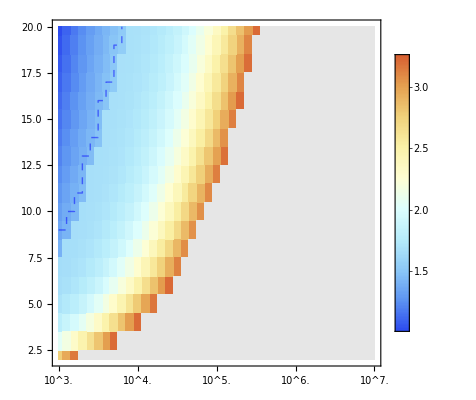

```mathematica
(* Construct plot *)

logBarMinMax={1,Log[Log[2*10^11]]};

frameTicksStyling={
{Automatic,None},
{Table[{NTEXP,If[Mod[NTEXP,1]==0,Superscript[10,ToString[NTEXP]],""]},{NTEXP,3,7,0.2}],None}};

plotTExtPanelB=
Show[
ListDensityPlot[TExtTable,InterpolationOrder->0,PlotRange->{All,All,logBarMinMax},PlotLegends->Automatic,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),FrameTicks->frameTicksStyling,
FrameTicksStyle->{{18,18},{18,18}},ImageSize->400],
ListContourPlot[NeutralLimitTable,PlotRange->All,InterpolationOrder->1,Contours->{-1,1},ContourShading->None,ContourStyle->Directive[{Thick,Blue,Dashed}]],
ListContourPlot[OldLimitTable,PlotRange->All,InterpolationOrder->0,Contours->{-1,1},ContourShading->{{Lighter[LightGray]},{None}}]
]
```

```mathematica
plotLegend=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),logBarMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Column",
"Ticks"->{
{N[Log[Log[10^2]]],"10^2"},
{N[Log[Log[10^3]]],"10^3"},
{N[Log[Log[10^5]]],"10^5"},
{N[Log[Log[10^7]]],"10^7"},
{N[Log[Log[10^9]]],"10^9"},
{N[Log[Log[10^11]]],"10^11"}
}
,
TicksStyle->18,ImageSize->800]
```

#### c=0.99

```mathematica
TExtTable=Flatten[Table[Table[{NTEXP,M,0},{NTEXP,3,7,2/20}],{M,2,20,1}],1];
NeutralLimitTable=Flatten[Table[Table[{NTEXP,M,0},{NTEXP,3,7,2/20}],{M,2,20,1}],1];
OldLimitTable=Flatten[Table[Table[{NTEXP,M,0},{NTEXP,3,7,2/20}],{M,2,20,1}],1];

params={c->0.99,NT->NT,M->M,TMax->10^11};

For[i=1,i≤Length[TExtTable],i++,

params[[2]]=NT->10^TExtTable[[i,1]]+1.21;
params[[3]]=M->TExtTable[[i,2]];

TExtTable[[i,3]]=If[((dTExtdN[M]>0)/.params),N[Log[Log[N[TExt[M]/.θ->(1+c)/(1-c)/.params]]]],N[Log[Log[TExtNeutral[M]/.params]]]];
NeutralLimitTable[[i,3]]=If[((dTExtdN[M]>0)/.params),0,1];
OldLimitTable[[i,3]]=If[TExtTable[[i,3]]<Log[Log[TMax/.params]],0,1];

];
```

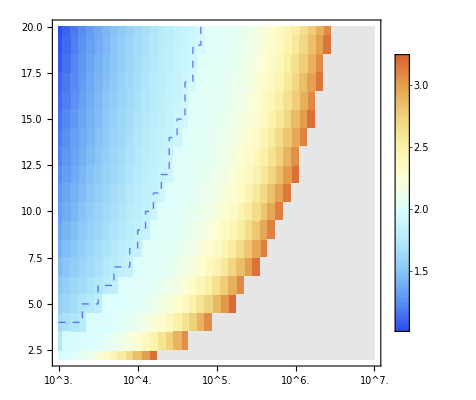

```mathematica
logBarMinMax={1,Log[Log[2*10^11]]};

frameTicksStyling={
{Automatic,None},
{Table[{NTEXP,If[Mod[NTEXP,1]==0,Superscript[10,ToString[NTEXP]],""]},{NTEXP,3,7,0.2}],None}};

plotTExtPanelC=
Show[
ListDensityPlot[TExtTable,InterpolationOrder->0,PlotRange->{All,All,logBarMinMax},PlotLegends->Automatic,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),FrameTicks->frameTicksStyling,
FrameTicksStyle->{{18,18},{18,18}},ImageSize->400],
ListContourPlot[NeutralLimitTable,PlotRange->All,InterpolationOrder->1,Contours->{-1,1},ContourShading->None,ContourStyle->Directive[{Thick,Blue,Dashed}]],
ListContourPlot[OldLimitTable,PlotRange->All,InterpolationOrder->0,Contours->{-1,1},ContourShading->{{Lighter[LightGray]},{None}}]
]
```

```mathematica
plotLegend=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),logBarMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Column",
"Ticks"->{
{N[Log[Log[10^2]]],"10^2"},
{N[Log[Log[10^3]]],"10^3"},
{N[Log[Log[10^5]]],"10^5"},
{N[Log[Log[10^7]]],"10^7"},
{N[Log[Log[10^9]]],"10^9"},
{N[Log[Log[10^11]]],"10^11"}
}
,
TicksStyle->18,ImageSize->800]
```

#### c=0.999

```mathematica
TExtTable=Flatten[Table[Table[{NTEXP,M,0},{NTEXP,3,7,2/20}],{M,2,20,1}],1];
NeutralLimitTable=Flatten[Table[Table[{NTEXP,M,0},{NTEXP,3,7,2/20}],{M,2,20,1}],1];
OldLimitTable=Flatten[Table[Table[{NTEXP,M,0},{NTEXP,3,7,2/20}],{M,2,20,1}],1];

params={c->0.999,NT->NT,M->M,TMax->10^11};

For[i=1,i≤Length[TExtTable],i++,

params[[2]]=NT->10^TExtTable[[i,1]]+1.21;
params[[3]]=M->TExtTable[[i,2]];

TExtTable[[i,3]]=If[((dTExtdN[M]>0)/.params),N[Log[Log[N[TExt[M]/.θ->(1+c)/(1-c)/.params]]]],N[Log[Log[TExtNeutral[M]/.params]]]];
NeutralLimitTable[[i,3]]=If[((dTExtdN[M]>0)/.params),0,1];
OldLimitTable[[i,3]]=If[TExtTable[[i,3]]<Log[Log[TMax/.params]],0,1];

];
```

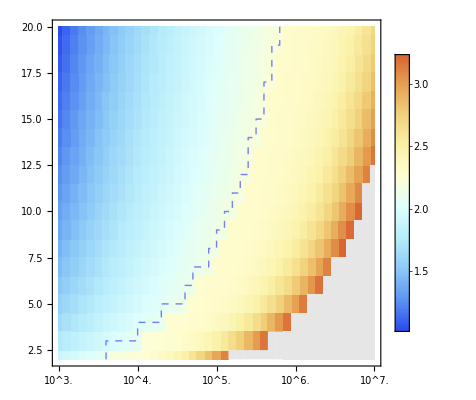

```mathematica
logBarMinMax={1,Log[Log[2*10^11]]};

frameTicksStyling={
{Automatic,None},
{Table[{NTEXP,If[Mod[NTEXP,1]==0,Superscript[10,ToString[NTEXP]],""]},{NTEXP,3,7,0.2}],None}};

plotTExtPanelD=
Show[
ListDensityPlot[TExtTable,InterpolationOrder->0,PlotRange->{All,All,logBarMinMax},PlotLegends->Automatic,ColorFunctionScaling->False,ColorFunction->((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),FrameTicks->frameTicksStyling,
FrameTicksStyle->{{18,18},{18,18}},ImageSize->400],
ListContourPlot[NeutralLimitTable,PlotRange->All,InterpolationOrder->1,Contours->{-1,1},ContourShading->None,ContourStyle->Directive[{Thick,Blue,Dashed}]],
ListContourPlot[OldLimitTable,PlotRange->All,InterpolationOrder->0,Contours->{-1,1},ContourShading->{{Lighter[LightGray]},{None}}]
]
```

```mathematica
plotLegend=BarLegend[{((ColorData["LightTemperatureMap"])[Rescale[#,logBarMinMax]]&),logBarMinMax},LegendMarkerSize->350,LabelStyle->18,LegendLayout->"Column",
"Ticks"->{
{N[Log[Log[10^2]]],"10^2"},
{N[Log[Log[10^3]]],"10^3"},
{N[Log[Log[10^5]]],"10^5"},
{N[Log[Log[10^7]]],"10^7"},
{N[Log[Log[10^9]]],"10^9"},
{N[Log[Log[10^11]]],"10^11"}
}
,
TicksStyle->18,ImageSize->800]
```

## Generate data for Table 1: Extinction times for specific species

```mathematica
r[M_]:=√(2 π)(2 m)/(1+c)√NT((M-1)/M)^(3/2-M)θ^(1/2+NT θ)((θ-1/M)/(θ-1/(M-1)))^(-1/2) ((θ-1/M)/(θ-1/(M-1)))^((1-M* θ)NT)(θ-1/(M-1))^(-NT*θ);
TExt[M_]:=1/NT(M-1)/m θ*r[M]/.θ->(1+c)/(1-c);
(* Time until the rth extinction starting with M mating types at equal frequency *)
TExtNeutral[M_]:=-NT*Sum[(-1)^(s-1)Binomial[M,s] s/M Log[s/M],{s,1,M-1}];

dTExtdN[M_]=D[TExt[M]/.θ->(1+c)/(1-c),NT];
dTExtdc[M_]=D[TExt[M]/.θ->(1+c)/(1-c),c];
dTExtdM[M_]=D[TExt[MD]/.θ->(1+c)/(1-c),MD]/.MD->M;
```

### Saccharomyces cerevisiae

```mathematica
(* Set parameter limits *)
mgMin=10^-8;
mgMax=10^-6;
NTMin=10^5;
NTMax=10^7;

params1={c->N[1-1/2000],Mmax->100,m->mgMin/NTMin,NT->NTMin,M->2};
params2={c->N[1-1/2000],Mmax->1000,m->mgMin/NTMax,NT->NTMax,M->2};
params3={c->N[1-1/2000],Mmax->100,m->mgMax/NTMin,NT->NTMin,M->2};
params4={c->N[1-1/2000],Mmax->100,m->mgMax/NTMax,NT->NTMax,M->2};
```

```mathematica
(* Calculate extinction upper and lower bounds on the extinction times *)

If[(dTExtdN[M]/.params1/.M->2)>0&&(dTExtdc[M]/.params1/.M->2)<0&&(dTExtdM[M]/.params1/.M->2)<0,Print[TExt[M]/.params1],Print[TExtNeutral[M]/.params1]]
If[(dTExtdN[M]/.params2/.M->2)>0&&(dTExtdc[M]/.params2/.M->2)<0&&(dTExtdM[M]/.params2/.M->2)<0,Print[TExt[M]/.params2],Print[TExtNeutral[M]/.params2]]
If[(dTExtdN[M]/.params3/.M->2)>0&&(dTExtdc[M]/.params3/.M->2)<0&&(dTExtdM[M]/.params3/.M->2)<0,Print[TExt[M]/.params3],Print[TExtNeutral[M]/.params3]]
If[(dTExtdN[M]/.params4/.M->2)>0&&(dTExtdc[M]/.params4/.M->2)<0&&(dTExtdM[M]/.params4/.M->2)<0,Print[TExt[M]/.params4],Print[TExtNeutral[M]/.params4]]

(* Check whether these results fall within the Neutral regime *)

If[(dTExtdN[M]/.params1/.M->2)>0&&(dTExtdc[M]/.params1/.M->2)<0&&(dTExtdM[M]/.params1/.M->2)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
If[(dTExtdN[M]/.params2/.M->2)>0&&(dTExtdc[M]/.params2/.M->2)<0&&(dTExtdM[M]/.params2/.M->2)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
If[(dTExtdN[M]/.params3/.M->2)>0&&(dTExtdc[M]/.params3/.M->2)<0&&(dTExtdM[M]/.params3/.M->2)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
If[(dTExtdN[M]/.params4/.M->2)>0&&(dTExtdc[M]/.params4/.M->2)<0&&(dTExtdM[M]/.params4/.M->2)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
```

1.47222×10^6

9.739×10^273

1.47222×10^6

9.739×10^273

(Non-neutral)

(Non-neutral)

(Non-neutral)

«1 more identical outputs»

### Chlamydomonas reinhardtii

```mathematica
(* Set parameter limits *)
mgMin=10^-8;
mgMax=10^-6;
NTMin=10^5;
NTMax=10^7;

params1={c->N[1-1/770],Mmax->100,m->mgMin/NTMin,NT->NTMin,M->2};
params2={c->N[1-1/770],Mmax->1000,m->mgMin/NTMax,NT->NTMax,M->2};
params3={c->N[1-1/770],Mmax->100,m->mgMax/NTMin,NT->NTMin,M->2};
params4={c->N[1-1/770],Mmax->100,m->mgMax/NTMax,NT->NTMax,M->2};
```

```mathematica
(* Calculate extinction upper and lower bounds on the extinction times *)

If[(dTExtdN[M]/.params1)>0&&(dTExtdc[M]/.params1)<0&&(dTExtdM[M]/.params1)<0,Print[N[TExt[M]/.params1]],Print[N[TExtNeutral[M]/.params1]]]
If[(dTExtdN[M]/.params2)>0&&(dTExtdc[M]/.params2)<0&&(dTExtdM[M]/.params2)<0,Print[N[TExt[M]/.params2]],Print[N[TExtNeutral[M]/.params2]]]
If[(dTExtdN[M]/.params3)>0&&(dTExtdc[M]/.params3)<0&&(dTExtdM[M]/.params3)<0,Print[N[TExt[M]/.params3]],Print[N[TExtNeutral[M]/.params3]]]
If[(dTExtdN[M]/.params4)>0&&(dTExtdc[M]/.params4)<0&&(dTExtdM[M]/.params4)<0,Print[N[TExt[M]/.params4]],Print[N[TExtNeutral[M]/.params4]]]

(* Check whether these results fall within the Neutral regime *)

If[(dTExtdN[M]/.params1/.M->2)>0&&(dTExtdc[M]/.params1/.M->2)<0&&(dTExtdM[M]/.params1/.M->2)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
If[(dTExtdN[M]/.params2/.M->2)>0&&(dTExtdc[M]/.params2/.M->2)<0&&(dTExtdM[M]/.params2/.M->2)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
If[(dTExtdN[M]/.params3/.M->2)>0&&(dTExtdc[M]/.params3/.M->2)<0&&(dTExtdM[M]/.params3/.M->2)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
If[(dTExtdN[M]/.params4/.M->2)>0&&(dTExtdc[M]/.params4/.M->2)<0&&(dTExtdM[M]/.params4/.M->2)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
```

7.72295×10^9

3.48×10^707

7.72295×10^9

3.48×10^707

(Non-neutral)

(Non-neutral)

(Non-neutral)

«1 more identical outputs»

### Tetrahymena (M_0=3)

```mathematica
(* Set parameter limits *)
mgMin=10^-8;
mgMax=10^-6;
NTMin=10^5;
NTMax=10^7;

params1={c->N[1-1/100],Mmax->100,m->mgMin/NTMin,NT->NTMin,M->3};
params2={c->N[1-1/100],Mmax->1000,m->mgMin/NTMax,NT->NTMax,M->3};
params3={c->N[1-1/100],Mmax->100,m->mgMax/NTMin,NT->NTMin,M->3};
params4={c->N[1-1/100],Mmax->100,m->mgMax/NTMax,NT->NTMax,M->3};
```

```mathematica
(* Calculate extinction upper and lower bounds on the extinction times *)

If[(dTExtdN[M]/.params1)>0&&(dTExtdc[M]/.params1)<0&&(dTExtdM[M]/.params1)<0,Print[N[TExt[M]/.params1]],Print[N[TExtNeutral[M]/.params1]]]
If[(dTExtdN[M]/.params2)>0&&(dTExtdc[M]/.params2)<0&&(dTExtdM[M]/.params2)<0,Print[N[TExt[M]/.params2]],Print[N[TExtNeutral[M]/.params2]]]
If[(dTExtdN[M]/.params3)>0&&(dTExtdc[M]/.params3)<0&&(dTExtdM[M]/.params3)<0,Print[N[TExt[M]/.params3]],Print[N[TExtNeutral[M]/.params3]]]
If[(dTExtdN[M]/.params4)>0&&(dTExtdc[M]/.params4)<0&&(dTExtdM[M]/.params4)<0,Print[N[TExt[M]/.params4]],Print[N[TExtNeutral[M]/.params4]]]

(* Check whether these results fall within the Neutral regime *)

If[(dTExtdN[M]/.params1)>0&&(dTExtdc[M]/.params1)<0&&(dTExtdM[M]/.params1)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
If[(dTExtdN[M]/.params2)>0&&(dTExtdc[M]/.params2)<0&&(dTExtdM[M]/.params2)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
If[(dTExtdN[M]/.params3)>0&&(dTExtdc[M]/.params3)<0&&(dTExtdM[M]/.params3)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
If[(dTExtdN[M]/.params4)>0&&(dTExtdc[M]/.params4)<0&&(dTExtdM[M]/.params4)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
```

1.33812×10^20

1.2906×10^1822

1.33812×10^20

1.2906×10^1822

(Non-neutral)

(Non-neutral)

(Non-neutral)

«1 more identical outputs»

### Tetrahymena (M_0=9)

```mathematica
(* Parameter limits *)
mgMin=10^-8;
mgMax=10^-6;
NTMin=10^5;
NTMax=10^7;

params1={c->N[1-1/100],Mmax->100,m->mgMin/NTMin,NT->NTMin,M->9};
params2={c->N[1-1/100],Mmax->100,m->mgMin/NTMax,NT->NTMax,M->9};
params3={c->N[1-1/100],Mmax->100,m->mgMax/NTMin,NT->NTMin,M->9};
params4={c->N[1-1/100],Mmax->100,m->mgMax/NTMax,NT->NTMax,M->9};
```

```mathematica
(* Calculate extinction upper and lower bounds on the extinction times *)

If[(dTExtdN[M]/.params1)>0&&(dTExtdc[M]/.params1)<0&&(dTExtdM[M]/.params1)<0,Print[N[TExt[M]/.params1]],Print[N[TExtNeutral[M]/.params1]]]
If[(dTExtdN[M]/.params2)>0&&(dTExtdc[M]/.params2)<0&&(dTExtdM[M]/.params2)<0,Print[N[TExt[M]/.params2]],Print[N[TExtNeutral[M]/.params2]]]
If[(dTExtdN[M]/.params3)>0&&(dTExtdc[M]/.params3)<0&&(dTExtdM[M]/.params3)<0,Print[N[TExt[M]/.params3]],Print[N[TExtNeutral[M]/.params3]]]
If[(dTExtdN[M]/.params4)>0&&(dTExtdc[M]/.params4)<0&&(dTExtdM[M]/.params4)<0,Print[N[TExt[M]/.params4]],Print[N[TExtNeutral[M]/.params4]]]

(* Check whether these results fall within the Neutral regime *)

If[(dTExtdN[M]/.params1)>0&&(dTExtdc[M]/.params1)<0&&(dTExtdM[M]/.params1)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
If[(dTExtdN[M]/.params2)>0&&(dTExtdc[M]/.params2)<0&&(dTExtdM[M]/.params2)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
If[(dTExtdN[M]/.params3)>0&&(dTExtdc[M]/.params3)<0&&(dTExtdM[M]/.params3)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
If[(dTExtdN[M]/.params4)>0&&(dTExtdc[M]/.params4)<0&&(dTExtdM[M]/.params4)<0,Print["(Non-neutral)"],Print["(Neutral)"]]
```

14204.

1.78114×10^153

14204.

1.78114×10^153

(Non-neutral)

(Non-neutral)

(Non-neutral)

«1 more identical outputs»

### Schizophyllum commune (M_0=23,328)

```mathematica
(* Parameter limits *)
mgMin=10^-8;
mgMax=10^-6;
NTMin=10^5;
NTMax=10^7;

params1={c->N[0],Mmax->100,m->mgMin/NTMin,NT->NTMin,M->23328};
params2={c->N[0],Mmax->100,m->mgMin/NTMax,NT->NTMax,M->23328};
params3={c->N[0],Mmax->100,m->mgMax/NTMin,NT->NTMin,M->23328};
params4={c->N[0],Mmax->100,m->mgMax/NTMax,NT->NTMax,M->23328};

(* Calculate extinction upper and lower bounds on the extinction times and Check whether these results fall within the Neutral regime *)

(* NOTE: large values of M mean that the numerical evaluation of Eq. 19 below requires extra working precision libraries *)

(* NOTE: For M=23,328, evaluation of the expressions becomes very time consuming  *)
If[(dTExtdN[M]/.params1)>0&&(dTExtdc[M]/.params1)<0&&(dTExtdM[M]/.params1)<0,Print["Non-neutral"],Print["Neutral"]]
Print[  Block[{$MaxExtraPrecision=15000},N[TExtNeutral[M]/.params1,20]]  ]

If[(dTExtdN[M]/.params4)>0&&(dTExtdc[M]/.params4)<0&&(dTExtdM[M]/.params4)<0,Print["Non-neutral"],Print["Neutral"]]
Print[  Block[{$MaxExtraPrecision=15000},N[TExtNeutral[M]/.params4,20]]  ]
```

Neutral

0.4084845031422389522

Neutral

40.84845031422389522

### Schizophyllum commune (M_0=288)

```mathematica
(* Parameter limits *)
mgMin=10^-8;
mgMax=10^-6;
NTMin=10^5;
NTMax=10^7;

params1={c->N[0],Mmax->100,m->mgMin/NTMin,NT->NTMin,M->288};
params2={c->N[0],Mmax->100,m->mgMin/NTMax,NT->NTMax,M->288};
params3={c->N[0],Mmax->100,m->mgMax/NTMin,NT->NTMin,M->288};
params4={c->N[0],Mmax->100,m->mgMax/NTMax,NT->NTMax,M->288};

(* Calculate extinction upper and lower bounds on the extinction times and Check whether these results fall within the Neutral regime *)

(* NOTE: large values of M mean that the numerical evaluation of Eq. 19 below requires extra working precision libraries *)

If[(dTExtdN[M]/.params1)>0&&(dTExtdc[M]/.params1)<0&&(dTExtdM[M]/.params1)<0,Print["Non-neutral"],Print["Neutral"]]
If[(dTExtdN[M]/.params1)>0&&(dTExtdc[M]/.params1)<0&&(dTExtdM[M]/.params1)<0,Print[N[TExt[M]/.params1]],Print[  Block[{$MaxExtraPrecision=1400},N[TExtNeutral[M]/.params1,20]]  ]]

If[(dTExtdN[M]/.params2)>0&&(dTExtdc[M]/.params2)<0&&(dTExtdM[M]/.params2)<0,Print["Non-neutral"],Print["Neutral"]]
If[(dTExtdN[M]/.params2)>0&&(dTExtdc[M]/.params2)<0&&(dTExtdM[M]/.params2)<0,Print[N[TExt[M]/.params2]],Print[N[TExtNeutral[M]/.params2]]]

If[(dTExtdN[M]/.params3)>0&&(dTExtdc[M]/.params3)<0&&(dTExtdM[M]/.params3)<0,Print["Non-neutral"],Print["Neutral"]]
If[(dTExtdN[M]/.params1)>0&&(dTExtdc[M]/.params1)<0&&(dTExtdM[M]/.params1)<0,Print[N[TExt[M]/.params1]],Print[  Block[{$MaxExtraPrecision=1400},N[TExtNeutral[M]/.params1,20]]  ]]

If[(dTExtdN[M]/.params4)>0&&(dTExtdc[M]/.params4)<0&&(dTExtdM[M]/.params4)<0,Print["Non-neutral"],Print["Neutral"]]
If[(dTExtdN[M]/.params4)>0&&(dTExtdc[M]/.params4)<0&&(dTExtdM[M]/.params4)<0,Print[N[TExt[M]/.params4]],Print[N[TExtNeutral[M]/.params4]]]
```

Neutral

57.768336832215983161

Non-neutral

2.64888×10^26

Neutral

57.768336832215983161

Non-neutral

2.64888×10^26

### Schizophyllum commune (M_0=81)

```mathematica
(* Parameter limits *)
mgMin=10^-8;
mgMax=10^-6;
NTMin=10^5;
NTMax=10^7;

params1={c->N[0],Mmax->100,m->mgMin/NTMin,NT->NTMin,M->81};
params2={c->N[0],Mmax->100,m->mgMin/NTMax,NT->NTMax,M->81};
params3={c->N[0],Mmax->100,m->mgMax/NTMin,NT->NTMin,M->81};
params4={c->N[0],Mmax->100,m->mgMax/NTMax,NT->NTMax,M->81};
```

```mathematica
(* Calculate extinction upper and lower bounds on the extinction times and Check whether these results fall within the Neutral regime *)

(* NOTE: large values of M mean that the numerical evaluation of Eq. 19 below requires extra working precision libraries *)

If[(dTExtdN[M]/.params1)>0&&(dTExtdc[M]/.params1)<0&&(dTExtdM[M]/.params1)<0,Print["Non-neutral"],Print["Neutral"]]
If[(dTExtdN[M]/.params1)>0&&(dTExtdc[M]/.params1)<0&&(dTExtdM[M]/.params1)<0,Print[N[TExt[M]/.params1]],Print[N[TExtNeutral[M]/.params1,10]]]

If[(dTExtdN[M]/.params2)>0&&(dTExtdc[M]/.params2)<0&&(dTExtdM[M]/.params2)<0,Print["Non-neutral"],Print["Neutral"]]
If[(dTExtdN[M]/.params2)>0&&(dTExtdc[M]/.params2)<0&&(dTExtdM[M]/.params2)<0,Print[N[TExt[M]/.params2]],Print[N[TExtNeutral[M]/.params2,10]]]

If[(dTExtdN[M]/.params3)>0&&(dTExtdc[M]/.params3)<0&&(dTExtdM[M]/.params3)<0,Print["Non-neutral"],Print["Neutral"]]
If[(dTExtdN[M]/.params3)>0&&(dTExtdc[M]/.params3)<0&&(dTExtdM[M]/.params3)<0,Print[N[TExt[M]/.params3]],Print[N[TExtNeutral[M]/.params3,10]]]

If[(dTExtdN[M]/.params4)>0&&(dTExtdc[M]/.params4)<0&&(dTExtdM[M]/.params4)<0,Print["Non-neutral"],Print["Neutral"]]
If[(dTExtdN[M]/.params4)>0&&(dTExtdc[M]/.params4)<0&&(dTExtdM[M]/.params4)<0,Print[N[TExt[M]/.params4]],Print[N[TExtNeutral[M]/.params4,10]]]
```

Non-neutral

8149.53

Non-neutral

2.73690246636875×10^337

Non-neutral

8149.53

Non-neutral

2.73690246636875×10^337

## Eq. (S27): Quasi-stationary distribution for the mating type number around a fixed point

```mathematica
(* Define Σ^(M) (see Eq.(S22) and surrounding derivation) *)
Σ[M_]:=M/(1-c)Table[If[i==j,(1-c)(M-1)/M^2(1-1/M)+2c 1/M(1-1/M),-(1-c)1/M^2(1-1/M)-2c 1/M^2],{i,1,M-1},{j,1,M-1}];

(* Define the determinant of Σ^(M), |Σ^(M)| [see Eq. (S23)] *)
detΣ[M_]:=1/M((1+c)/(1-c)-1/M)^(M-1);

(* Define equation for P^(QST(M))(n), a normal distribution centered on the deterministic fixed point with variance matrix N Σ^(M)*)
PQS[n_]:=MultinormalDistribution[ConstantArray[NT/Length[DeleteCases[n,0]],Length[DeleteCases[n,0]]-1],NT*Σ[Length[DeleteCases[n,0]]]]
```

## Code for generating plots in Fig. S1

#### M=3

```mathematica
(* Define parameters for compiled c++ Gillespie simulation file PST_sim_compiled *)
params={c->0,Mmax->100,m->0,NT->420};

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;
minTimeStep=0;
maxTimeStep=100000;
M0=3;

(* Convert parameters into ordered string for output to Gillespie simulation *)
paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[ NT/.params ]<>" "<>ToString[ AccountingForm[m/.params] ]<>" "<>ToString[c/.params]<>" "<>ToString[M0];;

(* Run external compiled c++ code and store results *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"MT_sim_compiled "<>paramString,Number,RecordLists->True];
```

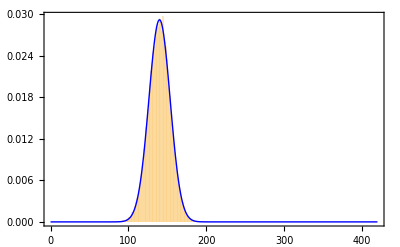

```mathematica
(* Calculate theoretical marginal distribution of PQS for ease of plotting (see Mathematica Section Eq.(S27):Quasi-stationary distribution for the mating type number around a fixed point) *)
nTable=Table[ToExpression["n"<>ToString[i]],{i,1,M0}];
PQSMarginal=Integrate[PDF[PQS[nTable]/.params,nTable[[1;;2]]],{n2,-∞,∞}];

(* Plot theoretical results against simulation results *)
Show[
Histogram[(simTraj[[All,3]]),{1},PDF,ChartStyle->Opacity[0.5],PlotRange->{{0,NT/.params},All},Frame->True,FrameStyle->18,ImageSize->400],
Plot[PQSMarginal,{n1,0,NT/.params},PlotStyle->{Blue,Thick},PlotRange->All]
]
```

#### M=4

```mathematica
(* Define parameters for compiled c++ Gillespie simulation file PST_sim_compiled *)
params={c->0,Mmax->100,m->0,NT->420};

output=1;
parmset=1;
run=1;
initialConditionSetting=0;
sampleRate=1;
minTimeStep=0;
maxTimeStep=100000;
M0=4;

(* Convert parameters into ordered string for output to Gillespie simulation *)
paramString=ToString[output]<>" "<>ToString[parmset]<>" "<>ToString[run]<>" "<>ToString[initialConditionSetting]<>" "<>ToString[sampleRate]<>" "<>ToString[minTimeStep]<>" "<>ToString[maxTimeStep]<>" "<>ToString[Mmax/.params]<>" "<>ToString[ NT/.params ]<>" "<>ToString[ AccountingForm[m/.params] ]<>" "<>ToString[c/.params]<>" "<>ToString[M0];;

(* Run external compiled c++ code and store results *)
simTraj=ReadList["!"<>NotebookDirectory[]<>"MT_sim_compiled "<>paramString,Number,RecordLists->True];
```

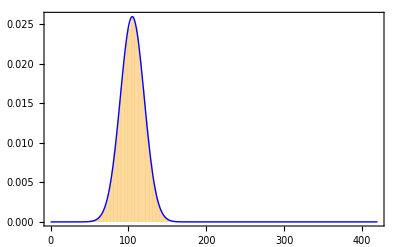

```mathematica
(* Calculate theoretical marginal distribution of PQS for ease of plotting (see Mathematica Section Eq.(S27):Quasi-stationary distribution for the mating type number around a fixed point) *)
nTable=Table[ToExpression["n"<>ToString[i]],{i,1,M0}];
PQSMarginal=Integrate[Integrate[PDF[PQS[nTable]/.params,nTable[[1;;3]]],{n2,-∞,∞}],{n3,-∞,∞}];

(* Plot theoretical results against simulation results *)
Show[
Histogram[(simTraj[[All,3]]),{1},PDF,ChartStyle->Opacity[0.5],PlotRange->{{0,NT/.params},All},Frame->True,FrameStyle->18,ImageSize->400],
Plot[PQSMarginal,{n1,0,NT/.params},PlotStyle->{Blue,Thick},PlotRange->All]
]
```

## Code for generating figure S4

```mathematica
(* Define the quasi-stationary distibution of the number of mating types calculated in the supplement [see Eq. S27] *)

Σ[M_]:=M/(1-c)Table[If[i==j,(1-c)(M-1)/M^2(1-1/M)+2c 1/M(1-1/M),-(1-c)1/M^2(1-1/M)-2c 1/M^2],{i,1,M-1},{j,1,M-1}];
detΣ[M_]:=1/M((1+c)/(1-c)-1/M)^(M-1);
PQS[n_]:=MultinormalDistribution[ConstantArray[NT/Length[DeleteCases[n,0]],Length[DeleteCases[n,0]]-1],NT*Σ[Length[DeleteCases[n,0]]]]
```

### c=0

```mathematica
(* Choose parameters for plot *)
params={NT->100,M->2,m->0,c->0.0001,Mmax->50,mutSD->0};

(* Define table measuring the height of the quasi-stationary distribution at its nearest extinction boundary relative to its central point - low values indicate a good approximation *)
quasiStationaryAtMMinus1Table=Flatten[Table[{NT,M,0},{NT,100,10100,1000},{M,2,20,2}],1];

(* Define table recording where we have observed the extinction time calculation to break down (see Eq. 20)*)
NeutralLimitTable=Flatten[Table[{NT,M,0},{NT,100,10100,1000},{M,2,20,2}],1];

(* Loop over N and M parameters *)
For[i=1,i≤Length[NeutralLimitTable],i++,

(* Set N and M parameters *)
params[[1]]=NT->NeutralLimitTable[[i,1]];
params[[2]]=M0->NeutralLimitTable[[i,2]];

(* Define a vector n with a length equal to the number of types *)
nTable=Table[ToExpression["n"<>ToString[i]],{i,1,M0/.params}];

(* Calculate the ratio of the prob. population is fixed point at NT/(M0-1) to that it is at NT/M0 for a Quasi-Stationary Distribution centered at NT/M0 *)

quasiStationaryAtMMinus1Table[[i,3]]=N[PDF[PQS[(Table[NT/M0/.params,{i,1,M0/.params}])],nTable[[1;;(M0-1/.params)]]]/.Table[nTable[[i]]->NT/(M0-1),{i,1,M0-1/.params}]/.params]/N[PDF[PQS[(Table[NT/M0/.params,{i,1,M0/.params}])],nTable[[1;;(M0-1/.params)]]]/.Table[nTable[[i]]->NT/M0,{i,1,M0-1/.params}]/.params];

(* Determine whether this region of parameter space is one in which we might expect Subscript[(T^Ext), M] or Subscript[(T^Neutral), M] to be valid (see Eq. 20) *)
NeutralLimitTable[[i,3]]=If[((dTExtdN[M0]>0)/.params)||((dTExtdM[M0]<0)/.params),0,1];

(* Periodically output how far this loop is along ... *)
If[Mod[i,20]==0,
Print["finished "<>ToString[i]];
];

]
```

finished 20

finished 40

finished 60

finished 80

finished 100

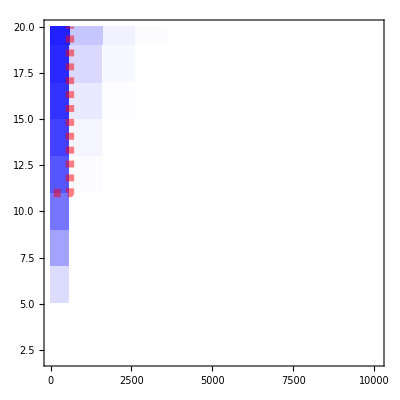

```mathematica
(* Generate plot to show that parameter regions in which the extinction time approximation Eq. 18 break down are also those in which the quasi-stationary distribution approximation break down *)

figS4A=Show[
ListDensityPlot[
quasiStationaryAtMMinus1Table,InterpolationOrder->0,FrameStyle->16,
PlotRange->{Automatic,{2,20},{0,1}},ColorFunctionScaling->False,ColorFunction->((Blend[{White,Blue}, #1] &)[Rescale[#,{0,1}]]&)],
ListContourPlot[NeutralLimitTable,PlotRange->All,InterpolationOrder->2,Contours->{-0.5,0.5},ContourShading->None,ContourStyle->Directive[{Thickness[0.015],Red,Dashed}]]
]
figS4Legend=BarLegend[{((Blend[{White,Blue}, #1] &)[Rescale[#,{0,1}]]&),{0,1}},LegendMarkerSize->300,LabelStyle->18,LegendLabel->Style[Text["QSTη_M/(QSTη_(M - 1))"],16],
TicksStyle->18];
```

### c=0.9

```mathematica
params={NT->100,M->2,m->0,c->0.9,Mmax->50,mutSD->0};

quasiStationaryAtMMinus1Table=Flatten[Table[{NT,M,0},{NT,100,10100,1000},{M,2,20,2}],1];
NeutralLimitTable=Flatten[Table[{NT,M,0},{NT,100,10100,1000},{M,2,20,2}],1];

For[i=1,i≤Length[NeutralLimitTable],i++,

params[[1]]=NT->NeutralLimitTable[[i,1]];
params[[2]]=M0->NeutralLimitTable[[i,2]];

nTable=Table[ToExpression["n"<>ToString[i]],{i,1,M0/.params}];

quasiStationaryAtMMinus1Table[[i,3]]=N[PDF[PQS[(Table[NT/M0/.params,{i,1,M0/.params}])],nTable[[1;;(M0-1/.params)]]]/.Table[nTable[[i]]->NT/(M0-1),{i,1,M0-1/.params}]/.params]/N[PDF[PQS[(Table[NT/M0/.params,{i,1,M0/.params}])],nTable[[1;;(M0-1/.params)]]]/.Table[nTable[[i]]->NT/M0,{i,1,M0-1/.params}]/.params];

NeutralLimitTable[[i,3]]=If[((dTExtdN[M0]>0)/.params)||((dTExtdM[M0]<0)/.params),0,1];

If[Mod[i,20]==0,
Print["finished "<>ToString[i]];
];

]
```

finished 20

finished 40

finished 60

finished 80

finished 100

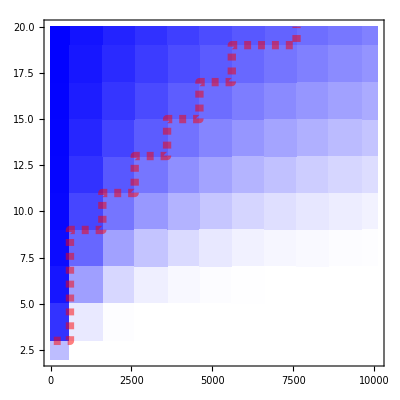

```mathematica
figS4B=Show[
ListDensityPlot[
quasiStationaryAtMMinus1Table,InterpolationOrder->0,FrameStyle->16,
PlotRange->{Automatic,{2,20},{0,1}},ColorFunctionScaling->False,ColorFunction->((Blend[{White,Blue}, #1] &)[Rescale[#,{0,1}]]&)],
ListContourPlot[NeutralLimitTable,PlotRange->All,InterpolationOrder->2,Contours->{-0.5,0.5},ContourShading->None,ContourStyle->Directive[{Thickness[0.015],Red,Dashed}]]
]
figS4Legend=BarLegend[{((Blend[{White,Blue}, #1] &)[Rescale[#,{0,1}]]&),{0,1}},LegendMarkerSize->300,LabelStyle->18,LegendLabel->Style[Text["QSTη_M/(QSTη_(M - 1))"],16],
TicksStyle->18];
```

### c=0.99

```mathematica
params={NT->100,M->2,m->0,c->0.99,Mmax->50,mutSD->0};

quasiStationaryAtMMinus1Table=Flatten[Table[{NT,M,0},{NT,100,10100,1000},{M,2,20,2}],1];
NeutralLimitTable=Flatten[Table[{NT,M,0},{NT,100,10100,1000},{M,2,20,2}],1];

For[i=1,i≤Length[NeutralLimitTable],i++,

params[[1]]=NT->NeutralLimitTable[[i,1]];
params[[2]]=M0->NeutralLimitTable[[i,2]];

nTable=Table[ToExpression["n"<>ToString[i]],{i,1,M0/.params}];

quasiStationaryAtMMinus1Table[[i,3]]=N[PDF[PQS[(Table[NT/M0/.params,{i,1,M0/.params}])],nTable[[1;;(M0-1/.params)]]]/.Table[nTable[[i]]->NT/(M0-1),{i,1,M0-1/.params}]/.params]/N[PDF[PQS[(Table[NT/M0/.params,{i,1,M0/.params}])],nTable[[1;;(M0-1/.params)]]]/.Table[nTable[[i]]->NT/M0,{i,1,M0-1/.params}]/.params];
NeutralLimitTable[[i,3]]=If[((dTExtdN[M0]>0)/.params)||((dTExtdM[M0]<0)/.params),0,1];

If[Mod[i,20]==0,
Print["finished "<>ToString[i]];
];

]
```

finished 20

finished 40

finished 60

finished 80

finished 100

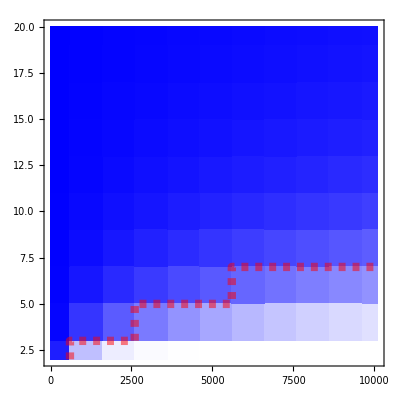

```mathematica
figS4C=Show[
ListDensityPlot[
quasiStationaryAtMMinus1Table,InterpolationOrder->0,FrameStyle->16,
PlotRange->{Automatic,{2,20},{0,1}},ColorFunctionScaling->False,ColorFunction->((Blend[{White,Blue}, #1] &)[Rescale[#,{0,1}]]&)],
ListContourPlot[NeutralLimitTable,PlotRange->All,InterpolationOrder->2,Contours->{-0.5,0.5},ContourShading->None,ContourStyle->Directive[{Thickness[0.015],Red,Dashed}]]
]
figS4Legend=BarLegend[{((Blend[{White,Blue}, #1] &)[Rescale[#,{0,1}]]&),{0,1}},LegendMarkerSize->300,LabelStyle->18,LegendLabel->Style[Text["QSTη_M/(QSTη_(M - 1))"],16],
TicksStyle->18];
```

### c=0.999

```mathematica
params={NT->100,M->2,m->0,c->0.999,Mmax->50,mutSD->0};

quasiStationaryAtMMinus1Table=Flatten[Table[{NT,M,0},{NT,100,10100,1000},{M,2,20,2}],1];
NeutralLimitTable=Flatten[Table[{NT,M,0},{NT,100,10100,1000},{M,2,20,2}],1];

For[i=1,i≤Length[NeutralLimitTable],i++,

params[[1]]=NT->NeutralLimitTable[[i,1]];
params[[2]]=M0->NeutralLimitTable[[i,2]];

nTable=Table[ToExpression["n"<>ToString[i]],{i,1,M0/.params}];

(* Ratio of prob I'm at the fixed point at NT/(M0-1) to that I'm at NT/M0 for a Quasi-Stationary Distribution centered at NT/M0 *)

quasiStationaryAtMMinus1Table[[i,3]]=N[PDF[PQS[(Table[NT/M0/.params,{i,1,M0/.params}])],nTable[[1;;(M0-1/.params)]]]/.Table[nTable[[i]]->NT/(M0-1),{i,1,M0-1/.params}]/.params]/N[PDF[PQS[(Table[NT/M0/.params,{i,1,M0/.params}])],nTable[[1;;(M0-1/.params)]]]/.Table[nTable[[i]]->NT/M0,{i,1,M0-1/.params}]/.params];
NeutralLimitTable[[i,3]]=If[((dTExtdN[M0]>0)/.params)||((dTExtdM[M0]<0)/.params),0,1];

If[Mod[i,20]==0,
Print["finished "<>ToString[i]];
];

]
```

finished 20

finished 40

finished 60

finished 80

finished 100

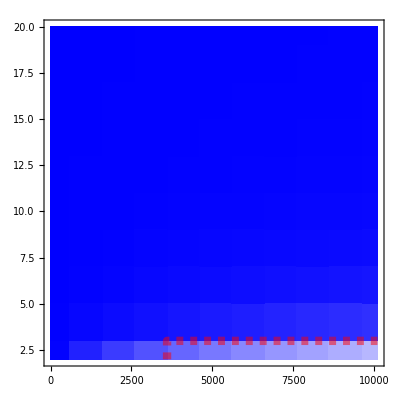

```mathematica
figS4D=Show[
ListDensityPlot[
quasiStationaryAtMMinus1Table,InterpolationOrder->0,FrameStyle->16,
PlotRange->{Automatic,{2,20},{0,1}},ColorFunctionScaling->False,ColorFunction->((Blend[{White,Blue}, #1] &)[Rescale[#,{0,1}]]&)],
ListContourPlot[NeutralLimitTable,PlotRange->All,InterpolationOrder->2,Contours->{-0.5,0.5},ContourShading->None,ContourStyle->Directive[{Thickness[0.015],Red,Dashed}]]
]
figS4Legend=BarLegend[{((Blend[{White,Blue}, #1] &)[Rescale[#,{0,1}]]&),{0,1}},LegendMarkerSize->300,LabelStyle->18,LegendLabel->Style[Text["QSTη_M/(QSTη_(M - 1))"],16],
TicksStyle->18];
```

## Code for generating Fig. S5

### Saccharomyces cerevisiae

```mathematica
PSTMApprox[M_]:=(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT;
rApprox[M_]:=PSTMApprox[M]/PSTMApprox[M-1];

(* Define mCrit(M), the critical value of m needed for the mode of PstM to be at least M *)
mgCritApprox[M_]:=Collect[NT*m/rApprox[M],m];
```

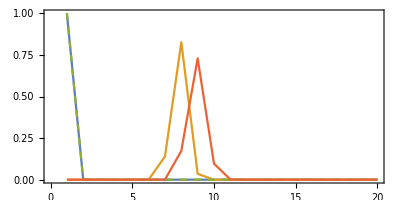

```mathematica
(* Define parameter bounds outlined in Fig. S5 (see also caption, Table 1.) *)
mgMin=10^-8;
mgMax=10^-6;
NTMin=10^5;
NTMax=10^7;

params1={c->N[1-1/2000],Mmax->100,m->mgMin/NTMin,NT->NTMin};
params2={c->N[1-1/2000],Mmax->1000,m->mgMin/NTMax,NT->NTMax};
params3={c->N[1-1/2000],Mmax->100,m->mgMax/NTMin,NT->NTMin};
params4={c->N[1-1/2000],Mmax->100,m->mgMax/NTMax,NT->NTMax};

(* Cycle through 4 parameter sets for plots *)

(* Params 1 *)
MAnaHistoTable1=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,1,20}];
MAnaHistoTable1=MAnaHistoTable1/.params1[[1]];
MAnaHistoTable1=MAnaHistoTable1/.params1[[3]];
MAnaHistoTable1=N[MAnaHistoTable1/.params1[[4]]];
normMAnaHistoTable1=Total[MAnaHistoTable1[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable1],i++,MAnaHistoTable1[[i,2]]=MAnaHistoTable1[[i,2]]/normMAnaHistoTable1];

(* Params 2 *)
MAnaHistoTable2=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,1,20}];
MAnaHistoTable2=MAnaHistoTable2/.params2[[1]];
MAnaHistoTable2=MAnaHistoTable2/.params2[[3]];
MAnaHistoTable2=N[MAnaHistoTable2/.params2[[4]]];
normMAnaHistoTable2=Total[MAnaHistoTable2[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable2],i++,MAnaHistoTable2[[i,2]]=MAnaHistoTable2[[i,2]]/normMAnaHistoTable2];

(* Params 3 *)
MAnaHistoTable3=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,1,20}];
MAnaHistoTable3=MAnaHistoTable3/.params3[[1]];
MAnaHistoTable3=MAnaHistoTable3/.params3[[3]];
MAnaHistoTable3=N[MAnaHistoTable3/.params3[[4]]];
normMAnaHistoTable3=Total[MAnaHistoTable3[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable3],i++,MAnaHistoTable3[[i,2]]=MAnaHistoTable3[[i,2]]/normMAnaHistoTable3];

(* Params 4 *)
MAnaHistoTable4=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,1,20}];
MAnaHistoTable4=MAnaHistoTable4/.params4[[1]];
MAnaHistoTable4=MAnaHistoTable4/.params4[[3]];
MAnaHistoTable4=N[MAnaHistoTable4/.params4[[4]]];
normMAnaHistoTable4=Total[MAnaHistoTable4[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable4],i++,MAnaHistoTable4[[i,2]]=MAnaHistoTable4[[i,2]]/normMAnaHistoTable4];

figS6A=ListLinePlot[{MAnaHistoTable1,MAnaHistoTable2,MAnaHistoTable3,MAnaHistoTable4},PlotRange->{{0,20},{0,1}},Frame->True,FrameStyle->18,ImageSize->400,PlotStyle->{Automatic,Automatic,Dashed,Automatic},AspectRatio->1/2]
figS6Legend=LineLegend[ColorData[97,"ColorList"][[1;;4]],{"m_g=10^-8, N=10^5","m_g=10^-8, N=10^7","m_g=10^-6, N=10^5","m_g=10^-6, N=10^7"}]
```

### Chlamydomonas reinhardtii

```mathematica
PSTMApprox[M_]:=(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT;
rApprox[M_]:=PSTMApprox[M]/PSTMApprox[M-1];

(* mCrit(M) is the critical value of m needed for the mode of PstM to be at least M *)

mgCritApprox[M_]:=Collect[NT*m/rApprox[M],m];
```

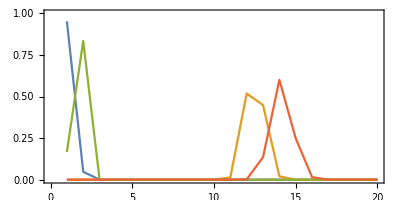

```mathematica
(* Parameter limits *)
mgMin=10^-8;
mgMax=10^-6;
NTMin=10^5;
NTMax=10^7;

params1={c->N[1-1/770],Mmax->100,m->mgMin/NTMin,NT->NTMin};
params2={c->N[1-1/770],Mmax->1000,m->mgMin/NTMax,NT->NTMax};
params3={c->N[1-1/770],Mmax->100,m->mgMax/NTMin,NT->NTMin};
params4={c->N[1-1/770],Mmax->100,m->mgMax/NTMax,NT->NTMax};

(* Params 1 *)
MAnaHistoTable1=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,1,20}];
MAnaHistoTable1=MAnaHistoTable1/.params1[[1]];
MAnaHistoTable1=MAnaHistoTable1/.params1[[3]];
MAnaHistoTable1=N[MAnaHistoTable1/.params1[[4]]];
normMAnaHistoTable1=Total[MAnaHistoTable1[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable1],i++,MAnaHistoTable1[[i,2]]=MAnaHistoTable1[[i,2]]/normMAnaHistoTable1];

(* Params 2 *)
MAnaHistoTable2=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,1,20}];
MAnaHistoTable2=MAnaHistoTable2/.params2[[1]];
MAnaHistoTable2=MAnaHistoTable2/.params2[[3]];
MAnaHistoTable2=N[MAnaHistoTable2/.params2[[4]]];
normMAnaHistoTable2=Total[MAnaHistoTable2[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable2],i++,MAnaHistoTable2[[i,2]]=MAnaHistoTable2[[i,2]]/normMAnaHistoTable2];

(* Params 3 *)
MAnaHistoTable3=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,1,20}];
MAnaHistoTable3=MAnaHistoTable3/.params3[[1]];
MAnaHistoTable3=MAnaHistoTable3/.params3[[3]];
MAnaHistoTable3=N[MAnaHistoTable3/.params3[[4]]];
normMAnaHistoTable3=Total[MAnaHistoTable3[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable3],i++,MAnaHistoTable3[[i,2]]=MAnaHistoTable3[[i,2]]/normMAnaHistoTable3];

(* Params 4 *)
MAnaHistoTable4=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,1,20}];
MAnaHistoTable4=MAnaHistoTable4/.params4[[1]];
MAnaHistoTable4=MAnaHistoTable4/.params4[[3]];
MAnaHistoTable4=N[MAnaHistoTable4/.params4[[4]]];
normMAnaHistoTable4=Total[MAnaHistoTable4[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable4],i++,MAnaHistoTable4[[i,2]]=MAnaHistoTable4[[i,2]]/normMAnaHistoTable4];

figS6B=ListLinePlot[{MAnaHistoTable1,MAnaHistoTable2,MAnaHistoTable3,MAnaHistoTable4},PlotRange->{{0,20},{0,1}},Frame->True,FrameStyle->18,ImageSize->400,AspectRatio->1/2]
```

### Tetrahymena

```mathematica
PSTMApprox[M_]:=(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT;
rApprox[M_]:=PSTMApprox[M]/PSTMApprox[M-1];

(* mCrit(M) is the critical value of m needed for the mode of PstM to be at least M *)

mgCritApprox[M_]:=Collect[NT*m/rApprox[M],m];
```

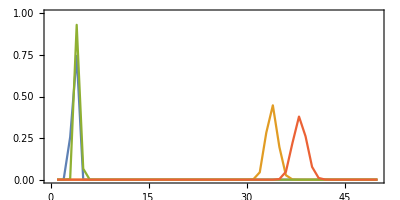

```mathematica
(* Parameter limits *)
mgMin=10^-8;
mgMax=10^-6;
NTMin=10^5;
NTMax=10^7;

params1={c->N[1-1/100],Mmax->100,m->mgMin/NTMin,NT->NTMin};
params2={c->N[1-1/100],Mmax->100,m->mgMin/NTMax,NT->NTMax};
params3={c->N[1-1/100],Mmax->100,m->mgMax/NTMin,NT->NTMin};
params4={c->N[1-1/100],Mmax->100,m->mgMax/NTMax,NT->NTMax};

(* Params 1 *)
MAnaHistoTable1=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,1,50}];
MAnaHistoTable1=MAnaHistoTable1/.params1[[1]];
MAnaHistoTable1=MAnaHistoTable1/.params1[[3]];
MAnaHistoTable1=N[MAnaHistoTable1/.params1[[4]]];
normMAnaHistoTable1=Total[MAnaHistoTable1[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable1],i++,MAnaHistoTable1[[i,2]]=MAnaHistoTable1[[i,2]]/normMAnaHistoTable1];

(* Params 2 *)
MAnaHistoTable2=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,1,50}];
MAnaHistoTable2=MAnaHistoTable2/.params2[[1]];
MAnaHistoTable2=MAnaHistoTable2/.params2[[3]];
MAnaHistoTable2=N[MAnaHistoTable2/.params2[[4]]];
normMAnaHistoTable2=Total[MAnaHistoTable2[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable2],i++,MAnaHistoTable2[[i,2]]=MAnaHistoTable2[[i,2]]/normMAnaHistoTable2];

(* Params 3 *)
MAnaHistoTable3=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,1,50}];
MAnaHistoTable3=MAnaHistoTable3/.params3[[1]];
MAnaHistoTable3=MAnaHistoTable3/.params3[[3]];
MAnaHistoTable3=N[MAnaHistoTable3/.params3[[4]]];
normMAnaHistoTable3=Total[MAnaHistoTable3[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable3],i++,MAnaHistoTable3[[i,2]]=MAnaHistoTable3[[i,2]]/normMAnaHistoTable3];

(* Params 4 *)
MAnaHistoTable4=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,1,50}];
MAnaHistoTable4=MAnaHistoTable4/.params4[[1]];
MAnaHistoTable4=MAnaHistoTable4/.params4[[3]];
MAnaHistoTable4=N[MAnaHistoTable4/.params4[[4]]];
normMAnaHistoTable4=Total[MAnaHistoTable4[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable4],i++,MAnaHistoTable4[[i,2]]=MAnaHistoTable4[[i,2]]/normMAnaHistoTable4];

figS6C=ListLinePlot[{MAnaHistoTable1,MAnaHistoTable2,MAnaHistoTable3,MAnaHistoTable4},PlotRange->{{0,50},{0,1}},Frame->True,FrameStyle->18,ImageSize->400,AspectRatio->1/2]
```

### Schizophyllum commune

```mathematica
PSTMApprox[M_]:=(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT;
rApprox[M_]:=PSTMApprox[M]/PSTMApprox[M-1];

(* mCrit(M) is the critical value of m needed for the mode of PstM to be at least M *)

mgCritApprox[M_]:=Collect[NT*m/rApprox[M],m];
```

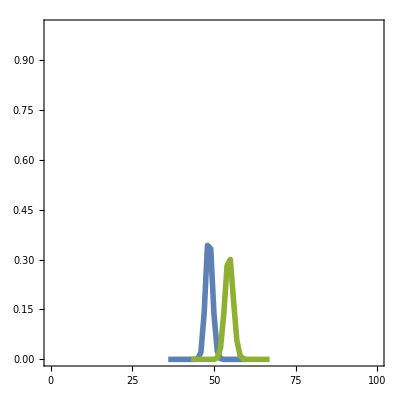

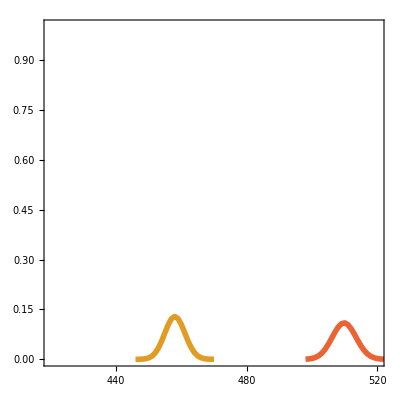

```mathematica
(* Parameter limits *)
mgMin=10^-8;
mgMax=10^-6;
NTMin=10^5;
NTMax=10^7;

params1={c->N[0],Mmax->100,m->mgMin/NTMin,NT->NTMin};
params2={c->N[0],Mmax->1000,m->mgMin/NTMax,NT->NTMax};
params3={c->N[0],Mmax->100,m->mgMax/NTMin,NT->NTMin};
params4={c->N[0],Mmax->100,m->mgMax/NTMax,NT->NTMax};

(* Params 1 *)
MAnaHistoTable1=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,48-12,48+12}];
MAnaHistoTable1=MAnaHistoTable1/.params1[[1]];
MAnaHistoTable1=MAnaHistoTable1/.params1[[3]];
MAnaHistoTable1=N[MAnaHistoTable1/.params1[[4]]];
normMAnaHistoTable1=Total[MAnaHistoTable1[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable1],i++,MAnaHistoTable1[[i,2]]=MAnaHistoTable1[[i,2]]/normMAnaHistoTable1];

(* Params 2 *)
MAnaHistoTable2=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,458-12,458+12}];
MAnaHistoTable2=MAnaHistoTable2/.params2[[1]];
MAnaHistoTable2=MAnaHistoTable2/.params2[[3]];
MAnaHistoTable2=N[MAnaHistoTable2/.params2[[4]]];
normMAnaHistoTable2=Total[MAnaHistoTable2[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable2],i++,MAnaHistoTable2[[i,2]]=MAnaHistoTable2[[i,2]]/normMAnaHistoTable2];

(* Params 3 *)
MAnaHistoTable3=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,55-12,55+12}];
MAnaHistoTable3=MAnaHistoTable3/.params3[[1]];
MAnaHistoTable3=MAnaHistoTable3/.params3[[3]];
MAnaHistoTable3=N[MAnaHistoTable3/.params3[[4]]];
normMAnaHistoTable3=Total[MAnaHistoTable3[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable3],i++,MAnaHistoTable3[[i,2]]=MAnaHistoTable3[[i,2]]/normMAnaHistoTable3];

(* Params 4 *)
MAnaHistoTable4=Table[{M,(2π)^(M/2-1)((2m)/(1+c))^(M-1)NT^((M-1)/2)M^(M-1/2)/(M!)(((1+c)/(1-c))^(M-1)/((1+c)/(1-c)-1/M))^(1/2)(((1+c)/(1-c)-1/M)(((1+c)/(1-c))/((1+c)/(1-c)-1/M))^(M((1+c)/(1-c))))^NT},{M,510-12,510+12}];
MAnaHistoTable4=MAnaHistoTable4/.params4[[1]];
MAnaHistoTable4=MAnaHistoTable4/.params4[[3]];
MAnaHistoTable4=N[MAnaHistoTable4/.params4[[4]]];
normMAnaHistoTable4=Total[MAnaHistoTable4[[All,2]]];
For[i=1,i≤Length[MAnaHistoTable4],i++,MAnaHistoTable4[[i,2]]=MAnaHistoTable4[[i,2]]/normMAnaHistoTable4];

figS6D1=ListLinePlot[{MAnaHistoTable1,MAnaHistoTable3},PlotRange->{{0,100},{0,1}},Frame->True,FrameStyle->36,ImageSize->400,AspectRatio->1,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thickness[0.01]},{ColorData[97,"ColorList"][[3]],Thickness[0.01]}}]
figS6D2=ListLinePlot[{MAnaHistoTable2,MAnaHistoTable4},PlotRange->{{420,520},{0,1}},Frame->True,FrameStyle->36,ImageSize->400,PlotStyle->{{ColorData[97,"ColorList"][[2]],Thickness[0.01]},{ColorData[97,"ColorList"][[4]],Thickness[0.01]}},AspectRatio->1,FrameTicks->{{Automatic,Automatic},{Table[{i,If[Mod[i,40]==0,ToString[i],""]},{i,420,520,5}],Automatic}}]
```